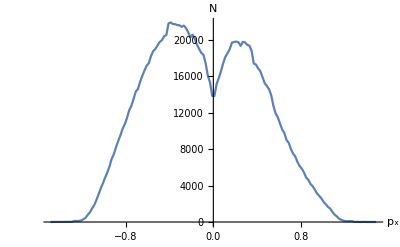

big3IIlinex.pdf

```mathematica
data=Import["C:\\Users\\hewenhao\\source\\repos\\第三次大作业II\\第三次大作业II\\line_temp_x.txt","Table"];
(*data=Table[data[[i]],{i,5,Length[data],2}];*)
show=Show[ListLinePlot[data,PlotRange->All],AxesLabel->{Subscript[p, x],N}]
Export["big3IIlinex.pdf",show]
```

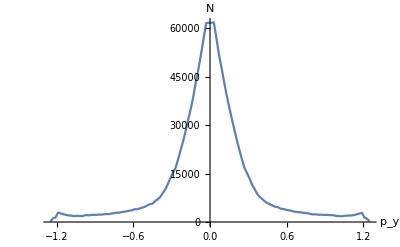

big3IIliney.pdf

```mathematica
data2=Import["C:\\Users\\hewenhao\\source\\repos\\第三次大作业II\\第三次大作业II\\line_temp_y.txt","Table"];
(*data2=Table[data2[[i]],{i,5,Length[data2],2}];*)
show2=Show[ListLinePlot[data2,PlotRange->All],AxesLabel->{Subscript[p, y],N}]
Export["big3IIliney.pdf",show2]
```

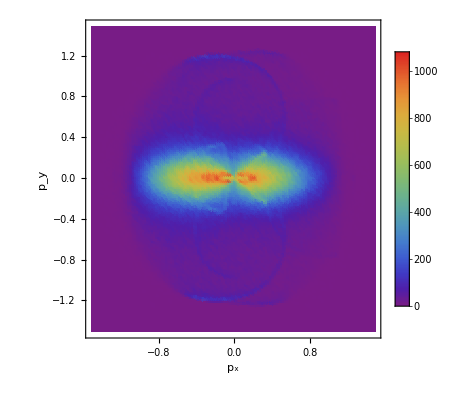

big3IIlinevec.pdf

```mathematica
datavec=Import["C:\\Users\\hewenhao\\source\\repos\\第三次大作业II\\第三次大作业II\\line_temp_vec.txt","Table"];
showvec=Show[ListDensityPlot[datavec,PlotLegends->Automatic,ColorFunction->"Rainbow",FrameLabel->{"p_x","p_y"},PlotRange->All]]
Export["big3IIlinevec.pdf",showvec]
```

```mathematica
SystemOpen["big3IIlinevec.pdf"]
```

```mathematica
SystemOpen["big3IIlinevec.pdf"]
```

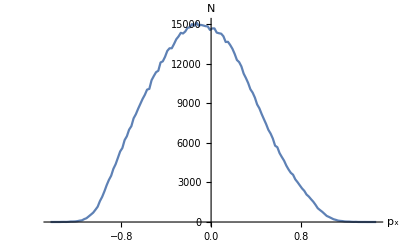

big3IIellix.pdf

```mathematica
data2elli=Import["C:\\Users\\hewenhao\\source\\repos\\第三次大作业II\\第三次大作业II\\elli_temp_x.txt","Table"];
show2elli=Show[ListLinePlot[data2elli,PlotRange->All],AxesLabel->{Subscript[p, x],N}]
Export["big3IIellix.pdf",show2elli]
```

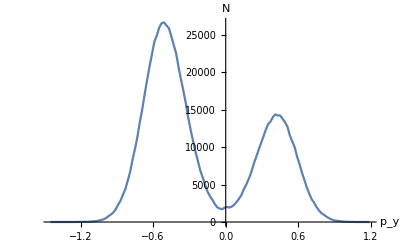

big3IIelliy.pdf

```mathematica
data2elliy=Import["C:\\Users\\hewenhao\\source\\repos\\第三次大作业II\\第三次大作业II\\elli_temp_y.txt","Table"];
show2elliy=Show[ListLinePlot[data2elliy,PlotRange->All],AxesLabel->{Subscript[p, y],N}]
Export["big3IIelliy.pdf",show2elliy]
```

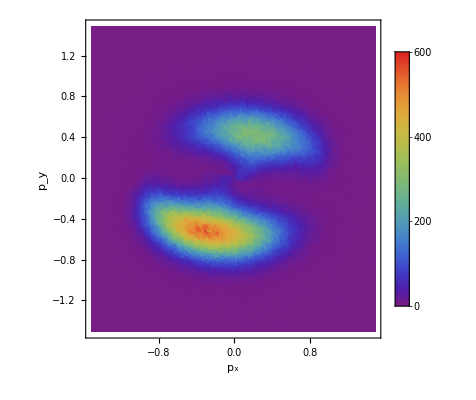

big3IIellivec.pdf

```mathematica
datavec2=Import["C:\\Users\\hewenhao\\source\\repos\\第三次大作业II\\第三次大作业II\\elli_temp_vec.txt","Table"];
showvec2=Show[ListDensityPlot[datavec2,PlotLegends->Automatic,ColorFunction->"Rainbow",FrameLabel->{"p_x","p_y"},PlotRange->All]]
Export["big3IIellivec.pdf",showvec2]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["big3IIellivec.pdf"]]]
```